# Neural Networks

#### Classification of randomly distributed data

```mathematica
sample[mean_,n_]:=RandomVariate[NormalDistribution[mean,1],n]
```

```mathematica
sample[0,10]
```

{1.3756,1.16563,0.728053,0.847254,0.40552,-0.982299,0.358429,-0.225515,-0.81566,1.09668}

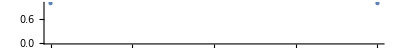

```mathematica
NumberLinePlot[{1,2}]
```

```mathematica
Manipulate[
clusters=sample[#,200]&/@{x,y,z};
NumberLinePlot[clusters,PlotRange->{-10,10}],
{x,-10,10},
{y,-10,10},
{z,-10,10}
]
```

MultinormalDistribution::vrprm: The value 1.52 at position 1 in MultinormalDistribution[1.52,{{1,0},{0,1}}] is expected to be a list of real numbers.

MultinormalDistribution::vrprm: The value -0.7 at position 1 in MultinormalDistribution[-0.7,{{1,0},{0,1}}] is expected to be a list of real numbers.

MultinormalDistribution::vrprm: The value 6.5 at position 1 in MultinormalDistribution[6.5,{{1,0},{0,1}}] is expected to be a list of real numbers.

General::stop: Further output of MultinormalDistribution::vrprm will be suppressed during this calculation.

RandomVariate::array: The array dimensions 200. given in position 2 of RandomVariate[MultinormalDistribution[1.52,{{1.,0},{0,1.}}],200.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomVariate::array: The array dimensions 200. given in position 2 of RandomVariate[MultinormalDistribution[-0.7,{{1.,0},{0,1.}}],200.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

General::stop: Further output of RandomVariate::array will be suppressed during this calculation.

MultinormalDistribution::vrprm: The value 1.52 at position 1 in MultinormalDistribution[1.52,{{1,0},{0,1}}] is expected to be a list of real numbers.

MultinormalDistribution::vrprm: The value -0.7 at position 1 in MultinormalDistribution[-0.7,{{1,0},{0,1}}] is expected to be a list of real numbers.

MultinormalDistribution::vrprm: The value 6.5 at position 1 in MultinormalDistribution[6.5,{{1,0},{0,1}}] is expected to be a list of real numbers.

General::stop: Further output of MultinormalDistribution::vrprm will be suppressed during this calculation.

RandomVariate::array: The array dimensions 200. given in position 2 of RandomVariate[MultinormalDistribution[1.52,{{1.,0},{0,1.}}],200.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomVariate::array: The array dimensions 200. given in position 2 of RandomVariate[MultinormalDistribution[-0.7,{{1.,0},{0,1.}}],200.] should be a list of non-negative machine-sized integers giving the dimensions for the result.

General::stop: Further output of RandomVariate::array will be suppressed during this calculation.

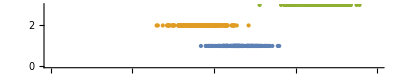

```mathematica
NumberLinePlot[clusters,PlotRange->{-10,10}]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->"Scalar",
"Output"->NetDecoder[{"Class",{"a","b","c"}}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
clusters//Dimensions
```

{3,200}

```mathematica
data=RandomSample[
Join[
Thread[clusters[[1]]->"a"],
Thread[clusters[[2]]->"b"],
Thread[clusters[[3]]->"c"]
]];
```

```mathematica
RandomSample[data,10]//Column
```

0.816353→a
2.01773→a
7.67523→c
0.247333→b
1.54578→a
6.86756→c
1.20733→a
6.23874→c
0.542008→a
1.20412→a

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
net[1.0]
```

a

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->10^6]
```

NetChain[]

```mathematica
NumberLinePlot[clusters,PlotRange->{-10,10}]
```

-Graphics-

```mathematica
result[7.0]
```

c

```mathematica
result[-3.0]
```

b

```mathematica
result[3.0,{"Probability","a"}]
```

0.972734

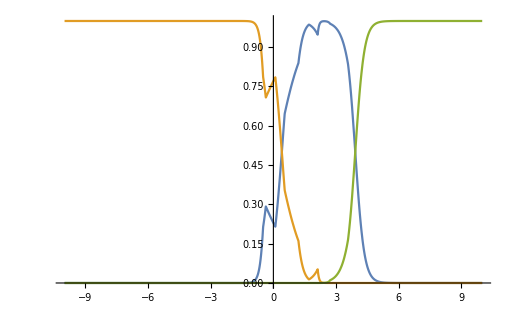

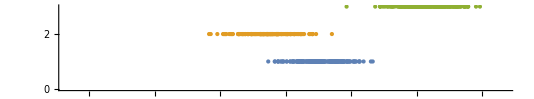

```mathematica
Plot[{
result[x,{"Probability","a"}],
result[x,{"Probability","b"}],
result[x,{"Probability","c"}]
},{x,-10,10}]
```

```mathematica
<|"a"->1,"b"->2|>
```

<|a→1,b→2|>

```mathematica
Dataset[
Map[<|
"input"->#,
"predicted"->result[#],
"probabilities"->result[#,"Probabilities"]
|>&,
Range[-10,10,0.25]
]
]
```

Dataset[<>]

### two dimensional

```mathematica
sample[c_,n_]:=RandomVariate[MultinormalDistribution[c,IdentityMatrix[2]],n]
```

```mathematica
sample[{0,0},10]//Grid
```

0.659997 | 0.0895976
-0.901308 | 0.873544
0.979798 | -0.246437
-0.0621836 | -0.587926
-0.164538 | 0.956024
1.93042 | -0.662942
0.666877 | -0.917353
1.06057 | -0.10069
-0.415092 | 1.05599
-0.0765758 | 0.391539

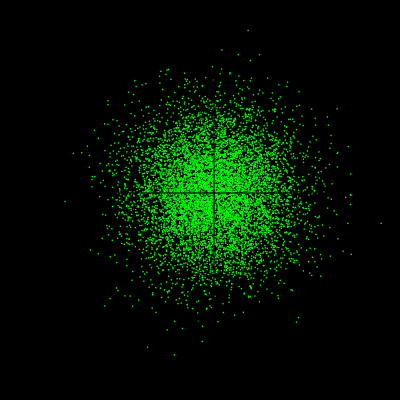

```mathematica
ListPlot[sample[{0,0},8000],Background->Black,PlotStyle->Green,AspectRatio->1,PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
clusters=sample[#,1000]&/@{{1.5,1},{-1.5,1},{0,-3}};
```

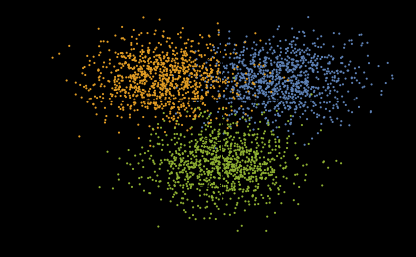

```mathematica
ListPlot[clusters,Background->Black]
```

```mathematica
net=NetChain[{
DotPlusLayer[30],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{"a","b","c"}}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
Total[{0.2,0.3,0.5}]
```

1.

```mathematica
data=RandomSample[
Join[
Thread[clusters[[1]]->"a"],
Thread[clusters[[2]]->"b"],
Thread[clusters[[3]]->"c"]
]];
```

```mathematica
data[[1]]
```

{-1.00203,-0.284523}→b

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result/@{{1.5,1},{-1.5,1},{0,-3}}
```

{a,b,c}

```mathematica
plotA=Plot3D[{
result[{x,y},{"Probability","a"}],
result[{x,y},{"Probability","b"}],
result[{x,y},{"Probability","c"}]
},{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
clusters[[1,1]]
```

```mathematica
{3.261067378210102,0.4243500345988651,1}
```

```mathematica
plotB=ListPointPlot3D[Map[Append[#,1]&,clusters,{2}],PlotStyle->{Yellow,Blue,Green}]
```

-Graphics3D-

```mathematica
Show[{plotA,plotB}]
```

-Graphics3D-